# Data requirements plots

This notebook computes the amount of control channel data required for soft and hard decision fusion type networks.

### Copyright notice

Copyright (C) 2012 Donagh Horgan.
Email: donaghh@rennes.ucc.ie.

This program is free software : you can redistribute it and/or modify
it under the terms of the GNU General Public License as published by
the Free Software Foundation, either version 3 of the License, or
(at your option) any later version.

This program is distributed in the hope that it will be useful,
but WITHOUT ANY WARRANTY; without even the implied warranty of
MERCHANTABILITY or FITNESS FOR A PARTICULAR PURPOSE. See 
COPYING for more details.

You should have received a copy of the GNU General Public License
along with this program. If not, see http://www.gnu.org/licenses.

### Version information

09/08/2012
1.0

### Changelog

Version 1.0: This version is similar to the version used in the presentation at CogART.

## Set up

Clear all symbol values and load function definitions:

```mathematica
ClearAll["Global`*"];
```

```mathematica
<<PlotLegends`
```

## Variables

Here, we define the parameters to be used:

```mathematica
n=10;
Nb=2;
```

```mathematica
fusionMethods={{"soft","equal"},{"soft","distinct"},{"hard","equal"},{"hard","distinct"},{"hard","approximation"}};
```

```mathematica
plotOptions={ImageSize->600,AxesLabel->{"N_b","Data (bits)"},PlotStyle->{{Black,Dotted},{Black,Dashed},{Black,DotDashed},Black,Black},GridLines->Automatic};
```

## Functions

Here, we define the data requirements function:

```mathematica
DataRequired[Nb_,n_,method_]:=Switch[method[[1]],
"soft",
Switch[method[[2]],
"equal",
Nb+Nb n,
"distinct",
2Nb n
],
"hard",
Switch[method[[2]],
"equal",
Nb+n,
"distinct",
2Nb n+n,
"approximation",
n
]
]
```

```mathematica
LegendFormat[method_]:=Switch[method[[1]],
"soft",
Switch[method[[2]],
"equal",
"Soft decision (equal SNR)",
"distinct",
"Soft decision (distinct SNR)"
],
"hard",
Switch[method[[2]],
"equal",
"Hard decision (equal SNR)",
"distinct",
"Hard decision (distinct SNR)",
"approximation",
"Approximation"
]
]
```

## Results

Data required versus number of bits:

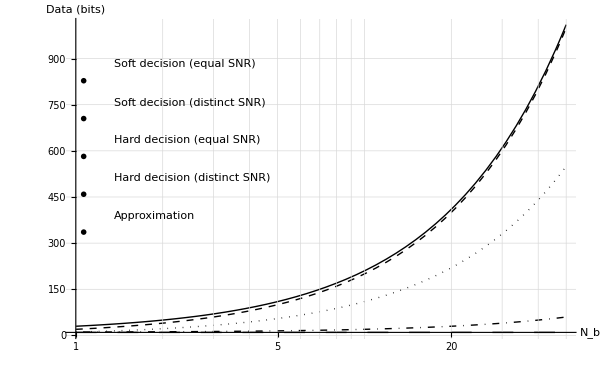

```mathematica
LogLinearPlot[Table[DataRequired[Nb0,n,m],{m,fusionMethods}]//Evaluate,{Nb0,1,50},ImageSize->600,PlotRange->Full,AxesLabel->{"N_b","Data (bits)"},PlotStyle->{{Black,Dotted},{Black,Dashed},{Black,DotDashed},Black,{Black,Dashing[0.025]}},GridLines->Automatic,PlotLegend->Table[LegendFormat[m],{m,fusionMethods}],LegendPosition->{-0.8,-0.25},LegendTextSpace->4,LegendShadow->None]
```

Data required versus network size:

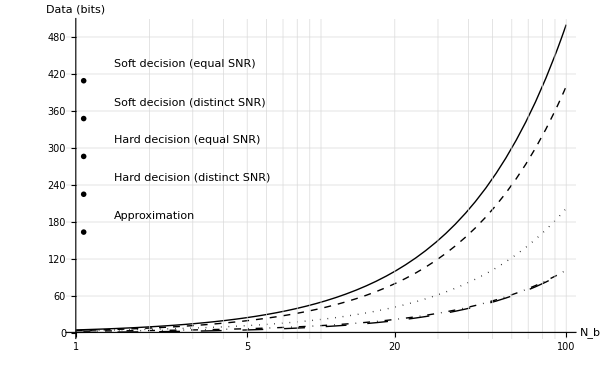

```mathematica
LogLinearPlot[Table[DataRequired[Nb,n0,m],{m,fusionMethods}]//Evaluate,{n0,1,100},ImageSize->600,PlotRange->Full,AxesLabel->{"N_b","Data (bits)"},PlotStyle->{{Black,Dotted},{Black,Dashed},{Black,DotDashed},Black,{Black,Dashing[0.025]}},GridLines->Automatic,PlotLegend->Table[LegendFormat[m],{m,fusionMethods}],LegendPosition->{-0.8,-0.25},LegendTextSpace->4,LegendShadow->None]
```